```mathematica
path = SystemDialogInput["FileOpen"];
```

```mathematica
image = Import[path];
```

```mathematica
getImageData[image_] := ImageData[image,"Byte"];
```

```mathematica
imageFromData[data_]:=Image[data,"Byte"];
```

```mathematica
getRGB[imageData_] := Flatten[imageData,{{3}, {1}, {2}}];
```

```mathematica
combineColor[r_]:=Flatten[r,{{2},{3},{1}}];
```

```mathematica
getTransformants[layer_] := Partition[layer, {8,8},8,{1,1},{-1}];
```

```mathematica
mergeTransformants[layer_] := Flatten[layer, {{1,3},{2,4}}];
```

```mathematica
normalize[t_] := Module[{f, result = t},(
f[row_] := row /;First[row] ==-1∨Last[row] !=-1;
f [row_]:= Module[{g, r}, (
g[{result_,last_},item_] := {Append[result,item],item} /; item ≠ -1;
g[{result_,last_}, item_]:= {Append[result,last],last};
 Fold[g,{{},-1},row] [[1]]
)];
result = f /@ result;
result = Flatten[result,{{2},{1}}];
result = f /@ result;
result = Flatten[result, {{2}, {1}}];

result
)];
```

```mathematica
restructure[t_] := FourierDCT[t];
```

```mathematica
reverseDCT[t_] := FourierDCT[t,3];
```

```mathematica
rounded[t_] := Map[Abs@Round@#&,t, {2}];
```

```mathematica
signs[t_] := Map[If[#>0,1,0]&,t,{2}];
```

```mathematica
applySigns[numbers_,signs_]:=Module[{result, f},(
result = {numbers, signs}~Flatten~{{2},{3}, {1}};

f[{n_,1}] := n;
f[{n_,0}] :=-n;

result = Map[f,result,{2}];

result
)];
```

```mathematica
bits[number_] := (
lastbit[x_]:= ⌈x/2⌉-⌊x/2⌋;
collectBits[x_,bits_] := collectBits[⌊x/2⌋,Append[bits,lastbit[x]]]/;x>0;
collectBits[x_,bits_] := bits /; x == 0;

collectBits[number,{}]
);
```

```mathematica
fromBits[b_]:=Module[{f, result},(
f[number_,bit_] := number*2 + bit;
result = Fold[f,0,Reverse @ b];

result
)];
```

```mathematica
bitcube[t_] := Module[{result = t}, (
result = Map[bits,result,{2}] // PadRight;
result = Flatten[result,{{3},{1,2}}];

result
)];
```

```mathematica
foldCube[sequences_]:=Module[{planes, cube, result},(
planes = (Partition[#,√Length[#]])&/@ sequences;
cube = Flatten[planes,{{2},{3},{1}}];
result = Map[fromBits,cube,{2}];

result
)];
```

```mathematica
compressBits[bits_] := Module[{f,result},(
f[{fs_,cs_, pe_},ce_] := {fs,cs + 1, ce} /;ce ==pe;
f[{fs_,cs_,pe_},ce_] := {Append[fs,cs],1,ce}/; ce≠pe;

result = Fold[f,{{},1,0},bits];
result = Append[result[[1]],result[[2]]] ;

result
)];
```

```mathematica
decompressBits[s_]:=Module[{flat},(
flat[n_,{i_}] := Array[1&,n] /; Mod[i,2]==0;
flat[n_,{i_}] := Array[0&,n] /; Mod[i,2]==1;
MapIndexed[flat,s] // Flatten // Rest
)];
```

```mathematica
compressTransformant[t_] := Module[{result = t, signsMatrix},(
result = normalize[result];
result = restructure[result];

signsMatrix = signs[result];
result = rounded[result];
result = bitcube[result];
result = compressBits /@ result;

{result,signsMatrix}
)];
```

```mathematica
decompressTransformant[{r_,s_}] := Module[{result = r}, (
result=decompressBits /@ result;
result=foldCube[result];
result=applySigns[result,s];
result=reverseDCT[result];
result=Map[Round,result,{2}];

result
)];
```

```mathematica
compress[image_] := Module[{result =image,dimensions = ImageDimensions[image]},(
result = getImageData[result];
result = getRGB[result];
result = getTransformants /@ result;
result = Map[compressTransformant,result,{3}];

{dimensions,result}
)];
```

```mathematica
export[result_] := (
exportPath = SystemDialogInput["FileSave"];
Export[exportPath,result,"WDX"];
);
```

```mathematica
decompress[{dimensions_,r_}] := Module[{result =r},(
result = Map[decompressTransformant, result,{3}];
result = mergeTransformants /@ result;
result = combineColor[result];
result = imageFromData[result];
result = ImageCrop[result, dimensions];

result
)];
```

```mathematica
statsFromTransformant[s_] := Module[{g,f, result},(
g[{zeros_,ones_,m_},item_]:= {zeros,Append[ones,item],0}/;m ==1;
g[{zeros_,ones_,m_},item_]:= {Append[zeros,item],ones,1}/;m ==0;

f[seq_]:=Fold[g,{{},{},1},Rest@s] /; First[s] ==1;
f[seq_]:=Fold[g,{{First[s]-1},{},1},Rest@s];

result = f[s];
result={#1,#2}& @@ result;

result
)];
```

```mathematica
statsFromTransformant[{1,1,2}]
```

{{2},{1}}

```mathematica
collectStats[{_,r_}]:=Module[{result = r},(
result = Flatten[result, {{4},{1,2,3}}] // First;
result = Flatten[result,1];
result = statsFromTransformant /@ result;
result = Flatten[result, {{2},{1}}];
result = 
result
)];
```

```mathematica
c = image // compress;
```

```mathematica
stat = collectStats[c];
```

```mathematica
zeros = stat[[1]];
ones = stat[[2]];
```

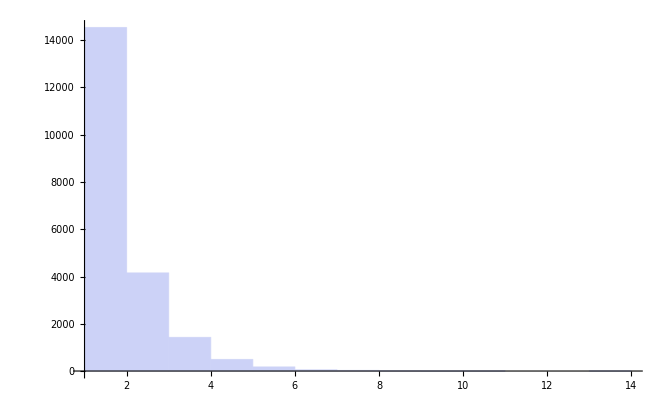

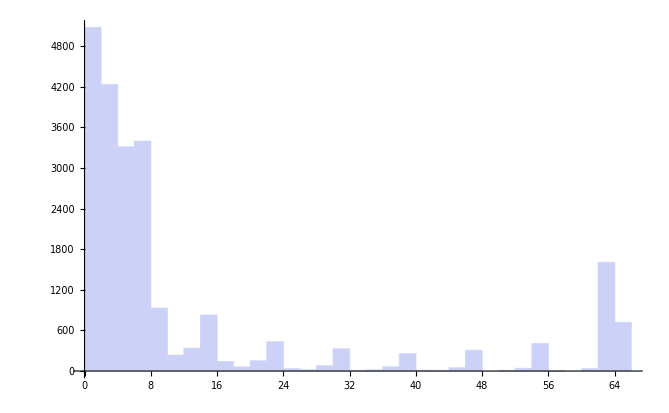

```mathematica
Histogram[ones]
Histogram[zeros]
```

```mathematica
restoredImage = image // compress // decompress;
```

```mathematica
image
ImageDifference[image, restoredImage]
restoredImage
```

-Graphics-

-Graphics-

-Graphics-